# Runtime Testing

```mathematica
<<CRNSSA`
```

rxn::shdw: Symbol rxn appears in multiple contexts {CRNSSA`,CRNSimulator`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

revrxn::shdw: Symbol revrxn appears in multiple contexts {CRNSSA`,CRNSimulator`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

init::shdw: Symbol init appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

GetSpecies::shdw: Symbol GetSpecies appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

DirectSSA::shdw: Symbol DirectSSA appears in multiple contexts {CRNSSA`,Global`}; definitions in context CRNSSA` may shadow or be shadowed by other definitions.

```mathematica
ConstructSys1[n_,type_]:=Module[
{rxns,xInits,yInits,inits},
rxns= Table[revrxn[x[i],y[i],RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
xInits=Table[type[x[i],RandomInteger[100]],{i,n}];
yInits=Table[type[y[i],RandomInteger[100]],{i,n}];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys2[n_,type_]:=Module[
{k,rxns,xInits,yInits,inits},
k=Round[Sqrt[n]];
rxns= Flatten[Table[revrxn[x[i]+x[j],y[i,j],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]];
xInits=Table[type[x[i],RandomInteger[100]],{i,k}];
yInits=Flatten[Table[type[y[i,j],RandomInteger[100]],{i,k},{j,k}]];
inits=Flatten[{xInits,yInits}];
{rxns,inits}]
```

```mathematica
ConstructSys3[n_,type_]:=Module[
{rxns,inits},
rxns= Table[revrxn[x,y,RandomReal[{1,10}],RandomReal[{1,10}]],{i,n}];
inits={type[x,RandomInteger[100]],type[y,RandomInteger[100]]};
{rxns,inits}]
```

```mathematica
TestSys[construction_,algo_,kRange_,iters_]:=Module[{type},
If[algo==="Opt",type=init,type=conc];
Table[Module[
{n,rxns,inits,rxnsys,nRxns,nSpecies,results,time,nIters,timePerIter},
n=k^2;
{rxns,inits} = construction[n,type];
rxnsys=Flatten[{rxns,inits}];
nRxns=Length[rxns];
nSpecies=If[algo==="Opt",
Length[GetSpecies[rxnsys]],
Length[SpeciesInRxnsys[rxnsys]]];
results=If[algo==="Opt",
Timing[DirectSSA[rxnsys,"useIter"->True,"iterEnd"->iters]],
Timing[SimulateRxnsysSSA[rxnsys,2/n]]];
time=results[[1]];
nIters=If[algo==="Opt",
iters,
Length[Normal[results[[2]]]]];
timePerIter=time/nIters;
{nRxns,nSpecies,time,nIters,timePerIter}],
kRange]]
```

```mathematica
algo="Opt";
kRange={k,1,25,4};
iters=1000;
resultsOpt1=TestSys[ConstructSys1,algo,kRange,iters]
resultsOpt2=TestSys[ConstructSys2,algo,kRange,iters]
resultsOpt3=TestSys[ConstructSys3,algo,kRange,iters]
```

{{2,2,0.,1000,0.},{50,50,0.015625,1000,0.000015625},{162,162,0.109375,1000,0.000109375},{338,338,0.40625,1000,0.00040625},{578,578,1.07813,1000,0.00107813},{882,882,2.3125,1000,0.0023125},{1250,1250,6.625,1000,0.006625}}

{{2,2,0.,1000,0.},{50,30,0.03125,1000,0.00003125},{162,90,0.125,1000,0.000125},{338,182,0.34375,1000,0.00034375},{578,306,0.796875,1000,0.000796875},{882,462,1.95313,1000,0.00195313},{1250,650,4.125,1000,0.004125}}

{{2,2,0.,1000,0.},{50,2,0.0625,1000,0.0000625},{162,2,0.09375,1000,0.00009375},{338,2,0.203125,1000,0.000203125},{578,2,0.4375,1000,0.0004375},{882,2,0.78125,1000,0.00078125},{1250,2,1.71875,1000,0.00171875}}

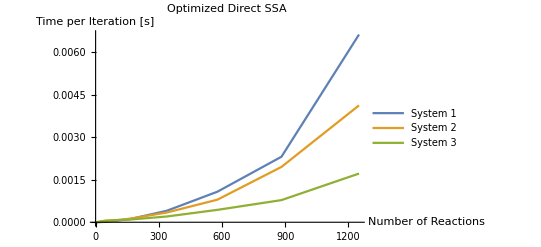

```mathematica
coorsOpt1nRxn=Table[{resultsOpt1[[i]][[1]],resultsOpt1[[i]][[5]]},{i,Length[resultsOpt1]}];
coorsOpt2nRxn=Table[{resultsOpt2[[i]][[1]],resultsOpt2[[i]][[5]]},{i,Length[resultsOpt2]}];
coorsOpt3nRxn=Table[{resultsOpt3[[i]][[1]],resultsOpt3[[i]][[5]]},{i,Length[resultsOpt3]}];
ListLinePlot[{coorsOpt1nRxn,coorsOpt2nRxn,coorsOpt3nRxn},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA"]
```

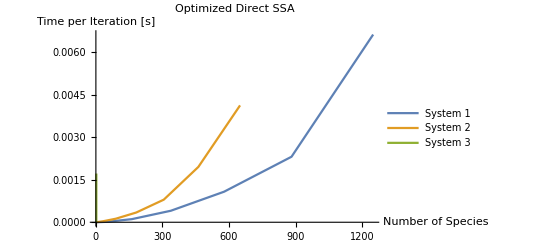

```mathematica
coorsOpt1nSpc=Table[{resultsOpt1[[i]][[2]],resultsOpt1[[i]][[5]]},{i,Length[resultsOpt1]}];
coorsOpt2nSpc=Table[{resultsOpt2[[i]][[2]],resultsOpt2[[i]][[5]]},{i,Length[resultsOpt2]}];
coorsOpt3nSpc=Table[{resultsOpt3[[i]][[2]],resultsOpt3[[i]][[5]]},{i,Length[resultsOpt3]}];
ListLinePlot[{coorsOpt1nSpc,coorsOpt2nSpc,coorsOpt3nSpc},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Species","Time per Iteration [s]"},"PlotLabel"->"Optimized Direct SSA"]
```

```mathematica
<<CRNSimulatorSSA`
```

```mathematica
algo="Naive";
kRange={k,1,25,4};
iters=1000;
resultsNaive1=TestSys[ConstructSys1,algo,kRange,iters]
resultsNaive2=TestSys[ConstructSys2,algo,kRange,iters]
resultsNaive3=TestSys[ConstructSys3,algo,kRange,iters]
```

{{2,2,0.265625,452,0.000587666},{50,50,0.78125,1272,0.00061419},{162,162,2.625,1137,0.00230871},{338,338,7.0625,1080,0.00653935},{578,578,9.57813,1095,0.00874715},{882,882,15.25,1097,0.0139015},{1250,1250,22.8906,1104,0.0207343}}

{{2,2,0.234375,4113,0.000056984},{50,30,1.07813,1351,0.00079802},{162,90,3.25,1342,0.00242176},{338,182,6.70313,1276,0.00525323},{578,306,11.9063,1608,0.00740438},{882,462,18.2344,1419,0.0128502},{1250,650,29.0313,1708,0.0169972}}

{{2,2,0.1875,2184,0.0000858516},{50,2,0.703125,1157,0.000607714},{162,2,2.04688,1270,0.00161171},{338,2,4.35938,1293,0.00337152},{578,2,7.28125,1616,0.00450572},{882,2,10.9063,643,0.0169615},{1250,2,16.7969,2146,0.00782706}}

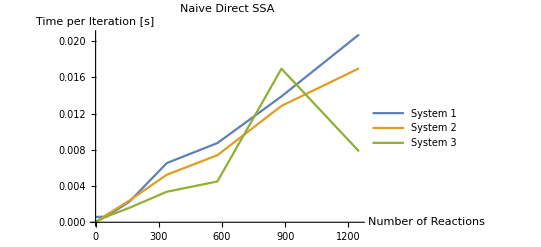

```mathematica
coorsNaive1nRxn=Table[{resultsNaive1[[i]][[1]],resultsNaive1[[i]][[5]]},{i,Length[resultsNaive1]}];
coorsNaive2nRxn=Table[{resultsNaive2[[i]][[1]],resultsNaive2[[i]][[5]]},{i,Length[resultsNaive2]}];
coorsNaive3nRxn=Table[{resultsNaive3[[i]][[1]],resultsNaive3[[i]][[5]]},{i,Length[resultsNaive3]}];
ListLinePlot[{coorsNaive1nRxn,coorsNaive2nRxn,coorsNaive3nRxn},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Naive Direct SSA"]
```

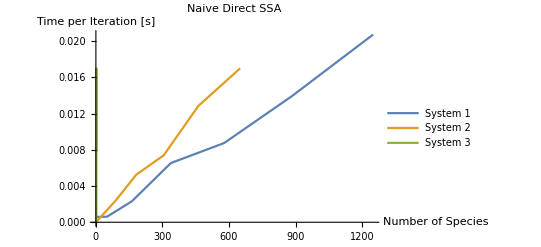

```mathematica
coorsNaive1nSpc=Table[{resultsNaive1[[i]][[2]],resultsNaive1[[i]][[5]]},{i,Length[resultsNaive1]}];
coorsNaive2nSpc=Table[{resultsNaive2[[i]][[2]],resultsNaive2[[i]][[5]]},{i,Length[resultsNaive2]}];
coorsNaive3nSpc=Table[{resultsNaive3[[i]][[2]],resultsNaive3[[i]][[5]]},{i,Length[resultsNaive3]}];
ListLinePlot[{coorsNaive1nSpc,coorsNaive2nSpc,coorsNaive3nSpc},PlotLegends->{"System 1","System 2","System 3"},AxesLabel->{"Number of Species","Time per Iteration [s]"},"PlotLabel"->"Naive Direct SSA"]
```

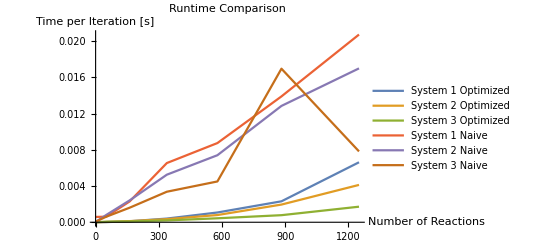

```mathematica
ListLinePlot[{coorsOpt1nRxn,coorsOpt2nRxn,coorsOpt3nRxn,coorsNaive1nRxn,coorsNaive2nRxn,coorsNaive3nRxn},PlotLegends->{"System 1 Optimized","System 2 Optimized","System 3 Optimized","System 1 Naive","System 2 Naive","System 3 Naive"},AxesLabel->{"Number of Reactions","Time per Iteration [s]"},"PlotLabel"->"Runtime Comparison"]
```

```mathematica
(*resultsNaive=Table[Module[{rxns= Flatten[Table[revrxn[x[i]+x[j],y[i,j],RandomReal[{1,10}],RandomReal[{1,10}]],{i,k},{j,k}]],
xInits=Table[conc[x[i],RandomInteger[100]],{i,k}],
yInits=Flatten[Table[conc[y[i,j],RandomInteger[100]],{i,k},{j,k}]],
rxnsys,results,nRxns,time,iters,timePerIter},
rxnsys = Flatten[{rxns,xInits,yInits}];
results=Timing[SimulateRxnsysSSA[rxnsys,100/(k^2)]];
nRxns=Length[rxns];
time=results[[1]];
iters=Length[Normal[results[[2]]]];
timePerIter=time/iters;
{nRxns,time,iters,timePerIter}],
{k,1,9,4}]*)
```

{{2,0.21875,32336,6.76491×10^-6},{32,1.10938,32853,0.0000337678}}